```mathematica
Quit[]
```

```mathematica
1+1
```

2

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m";
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m";
<<"/home/riccardo/Programs/ABISS/ABISS.m";
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish_var", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
process={F[3,{1,o}],-F[3,{1,o}]}->{F[2,{2}],-F[2,{2}]};
topologiesBorn=CreateTopologies[0,2->2,ExcludeTopologies->Tadpoles];
fieldsBorn=InsertFields[topologiesBorn, process];
topologies1L=CreateTopologies[1,2-> 2,ExcludeTopologies->{Tadpoles,WFCorrections}];
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish_var.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish_var} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 24 field point(s)

in total: 4 Particles insertions

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 43 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 49 Particles insertions

> Top. 13: 16 Particles insertions

> Top. 14: 20 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 34 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

> Top. 25: 0 Particles insertions

> Top. 26: 0 Particles insertions

> Top. 27: 0 Particles insertions

> Top. 28: 0 Particles insertions

> Top. 29: 0 Particles insertions

> Top. 30: 0 Particles insertions

> Top. 31: 0 Particles insertions

> Top. 32: 0 Particles insertions

> Top. 33: 0 Particles insertions

> Top. 34: 0 Particles insertions

> Top. 35: 0 Particles insertions

> Top. 36: 0 Particles insertions

> Top. 37: 0 Particles insertions

> Top. 38: 0 Particles insertions

> Top. 39: 0 Particles insertions

> Top. 40: 214 Particles insertions

> Top. 41: 0 Particles insertions

> Top. 42: 0 Particles insertions

Restoring 24 field point(s)

in total: 376 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

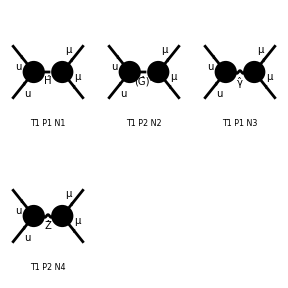

```mathematica
Paint[fieldsBorn];
```

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn,GaugeRules->{}];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

```mathematica
ampBorn[[2]]
```

FeynAmp[GraphID[Topology==1,Generic==1,Particles==2,Number==2],Integral[],-v̄[p2,MU].(EL gXuu MU om_--EL gXuu MU om_+).u[p1,MU] ū[k1,MM].(-EL gXll MM om_-+EL gXll MM om_+).v[k2,MM] 1/((k1+k2)^2-MZ^2 xi_bg)]

```mathematica
myAmpBorn=CalcFeynAmp[ampBorn[[0]][ampBorn[[2]]],FermionChains->Chiral]
```

preparing FORM code in /home/riccardo/fc-amp-1.frm

running FORM...

ok

Amp[{{F[3,{1,o}],k[1],MU,Qu},{-F[3,{1,o}],k[2],MU,-Qu}}→{{F[2,{2}],k[3],MM,{Ql,LeptonNumber}},{-F[2,{2}],k[4],MM,{-Ql,-LeptonNumber}}}][-4 Alfa gXll gXuu MM MU π Den[S,MZ2 Xbg] Mat[F1]+4 Alfa gXll gXuu MM MU π Den[S,MZ2 Xbg] Mat[F2]+4 Alfa gXll gXuu MM MU π Den[S,MZ2 Xbg] Mat[F3]-4 Alfa gXll gXuu MM MU π Den[S,MZ2 Xbg] Mat[F4]]

```mathematica
_Hel=0
```

0

```mathematica
a=SquaredME[myAmpBorn]//Simplify;
a=a/.HelicityME[a];
a=PolarizationSum[a]//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

4 Alfa2 gXll gXuu MM^2 MU^2 π^2 (2 MM^2-2 MM2+S) (2 MU^2-2 MU2+S) gXll^* gXuu^* Den[S,MZ2 Xbg] Den[S,MZ2 Xbg^*]

```mathematica
a=HelicityME[myAmpBorn,myAmpBorn]//PolarizationSum
```

> 64 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

preparing FORM code in /home/riccardo/fc-pol-1.frm

running FORM...

ok

0

```mathematica
HelicityME[myAmpBorn,myAmpBorn]
```

HelicityME::weyl: Warning: HelicityME does not work on WeylChains.  CalcFeynAmp uses DiracChains with the option FermionChains -> Chiral or VA.

> 16 helicity matrix elements

preparing FORM code in /home/riccardo/fc-hel-1.frm

running FORM...

ok

{Mat[F5,F5]→1/16 (MM2 (4 MU2-2 S)-2 MU2 S+S^2),Mat[F5,F7]→1/8 MU^2 (2 MM2-S),Mat[F5,F6]→1/8 MM^2 (2 MU2-S),Mat[F5,F8]→(MM^2 MU^2)/4,Mat[F6,F5]→1/8 MM^2 (2 MU2-S),Mat[F6,F7]→(MM^2 MU^2)/4,Mat[F6,F6]→1/16 (MM2 (4 MU2-2 S)-2 MU2 S+S^2),Mat[F6,F8]→1/8 MU^2 (2 MM2-S),Mat[F7,F5]→1/8 MU^2 (2 MM2-S),Mat[F7,F7]→1/16 (MM2 (4 MU2-2 S)-2 MU2 S+S^2),Mat[F7,F6]→(MM^2 MU^2)/4,Mat[F7,F8]→1/8 MM^2 (2 MU2-S),Mat[F8,F5]→(MM^2 MU^2)/4,Mat[F8,F7]→1/8 MM^2 (2 MU2-S),Mat[F8,F6]→1/8 MU^2 (2 MM2-S),Mat[F8,F8]→1/16 (MM2 (4 MU2-2 S)-2 MU2 S+S^2)}

```mathematica
a[[1]]/.a[[2]]
```

16 Alfa2 (F2+F3) (F1+F4) gHll gHuu MM^2 MU^2 π^2 (F2^*+F3^*) (F1^*+F4^*) gHll^* gHuu^* Den[S,MH2]^2

```mathematica
SubExpr[]
```

{}

```mathematica
Abbr[]
```

{F1→(v̇ 2|6|u1),F4→(v̇ 2|7|u1),F3→(u̇ 3|6|v4),F2→(u̇ 3|7|v4)}

```mathematica
_Hel=0
```

0

```mathematica
HelicityME[a]
```

HelicityME::weyl: Warning: HelicityME does not work on WeylChains.  CalcFeynAmp uses DiracChains with the option FermionChains -> Chiral or VA.

HelicityME::nomat: Warning: No matrix elements to compute.

{}

## Dirac Traces

```mathematica
GTr[a_,b_]:=4 SP[a,b]/;FreeQ[{b},G5]/;FreeQ[{a},G5];
GTr[G5]:=0;
GTr[x___,-G5,y___]:=-GTr[x,G5,y];
GTr[x___,G5,G5,y___]:=GTr[x,y];
GTr[x___,{a_},{a_},y___]:=myDim GTr[x,y];
GTr[x___,{a_},b__,{a_},y___]:=(-1)^Length[{b}]myDim GTr[x,b,y]+Sum[list={b}; tmp = Delete[list,i];(-1)^(i+1) 2 SP[list[[i]],{a}]GTr[x,Sequence@@ tmp, {a}, y],{i,Length[{b}]}]/;FreeQ[{b},G5];
GTr[a___,G5,b__]:=Module[{risultato},risultato=(-1)^Length[{b}] GTr[a,b,G5];risultato]/;FreeQ[{b},G5];
GTr[a___,G5,b__, G5]:=Module[{risultato},risultato=(-1)^Length[{b}] GTr[a,b];risultato]/;FreeQ[{b},G5];
GTr[x___,p_,b___,p_,y___]:=(-1)^Length[{b}]SP[p,p] GTr[x,b,y]+Sum[list={b}; tmp = Delete[list,i];(-1)^(i+1) 2 SP[list[[i]],p]GTr[x,Sequence@@ tmp, p, y],{i,Length[{b}]}]/;FreeQ[{b},G5]/;!ListQ[p];
GTr[x___,Times[-1,p_],b___,p_,y___]:=(-1)^Length[{b}](-SP[p,p]) GTr[x,b,y]-Sum[list={b}; tmp = Delete[list,i];(-1)^(i+1) 2 SP[list[[i]],p]GTr[x,Sequence@@ tmp, p, y],{i,Length[{b}]}]/;FreeQ[{b},G5]/;!ListQ[p];
GTr[x___,p_,b___,Times[-1,p_],y___]:=(-1)^Length[{b}](-SP[p,p]) GTr[x,b,y]-Sum[list={b}; tmp = Delete[list,i];(-1)^(i+1) 2 SP[list[[i]],p]GTr[x,Sequence@@ tmp, p, y],{i,Length[{b}]}]/;FreeQ[{b},G5]/;!ListQ[p];

GTr[x__,G5]:=0/;Length[{x}]<4;
```

```mathematica
GTr[p,q]
```

4 SP[p,q]

```mathematica
GTr[p1-m,G5,p2+m,G5]
```

-4 (-SP[m,m]+SP[m,p1]-SP[m,p2]+SP[p1,p2])

```mathematica
GTr[G5,G5]
```

GTr[]